```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
ρ[x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}];
Subscript[ρ, B][x_,y_,t_]=1/b[t]*ρ[x/b[t],y/b[t]]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
ℛ[x_,y_,t_]=1/b[t]*Subscript[ρ, F][x/b[t],y/b[t]]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
Subscript[n, B][p_,t_] :=Subscript[n, B][p,t]= 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, B][x,y,t],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->5,PrecisionGoal->5];
Subscript[n, R][p_,t_]:=2/(2*π)*NIntegrate[E^(-I*p*(y-x))*ℛ[x,y,t],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->3,PrecisionGoal->3];
Subscript[ρ, M][x_,y_]=(ⅇ^(1/2 (-x^2-3 y^2)) (-2 x-ⅇ^(y^2) √π (1+2 xy) Erf[y]))/(2 π);
Subscript[n, AB][p_]:=2/(2*π)*NIntegrate[E^(-I*p*(y-x))*Subscript[ρ, M][x,y],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->3,PrecisionGoal->3];
```

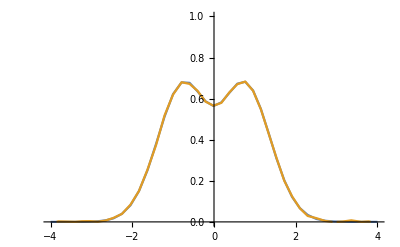

```mathematica
Plot[{Subscript[n, F][p],Subscript[n, R][p,6]},{p,-4,4},PlotRange->{0,1},PlotPoints->6,MaxRecursion->3]
```

NIntegrate::inumr: The integrand 1/2 (-ⅇ^(-x^2/2-y^2/2) √(2/π) x+ⅇ^(-x^2/2-y^2/2) √(2/π) y) Abs[-ⅇ^(-1/2 Power[«2»]-1/2 Power[«2»]) √(2/π) x+ⅇ^(-1/2 Power[«2»]-1/2 Power[«2»]) √(2/π) y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

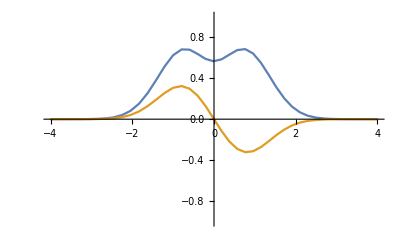

```mathematica
M[x_]=NIntegrate[Subscript[ψ, F][x,y,0]Abs[Subscript[ψ, F][x,y,0]],{y,-Infinity,Infinity}, AccuracyGoal->3,PrecisionGoal->3];
Plot[{2*Subscript[ρ, F][x,x],M[x]},{x,-4,4},PlotRange->{-1,1},PlotPoints->6,MaxRecursion->3]
```

```mathematica
Subscript[ψ, F][x,y,0]Abs[Subscript[ψ, F][x,y,0]]//FullSimplify
Subscript[n, M][x_]=Integrate[Subscript[ψ, F][x,y,0]Abs[Subscript[ψ, F][x,y,0]],{y,-Infinity,Infinity},Assumptions->{Im[x]==0,Im[z]==0}]//FullSimplify
h[p_]=2/π E^(-p^2)Integrate[E^(-x^2)Abs[x-Re[p]](x-Re[p]),{x,-Infinity,Infinity},Assumptions->Im[p]==0]//FullSimplify
```

-(ⅇ^(1/2 (-x^2-y^2-Re[x^2+y^2])) (x-y) Abs[x-y])/π

(ⅇ^(-2 x^2) (-4 x-2 ⅇ^(x^2) √π (1+2 x^2) Erf[x]))/(4 π)

(ⅇ^(-2 p^2) (-2 p-ⅇ^(p^2) (1+2 p^2) √π Erf[p]))/π

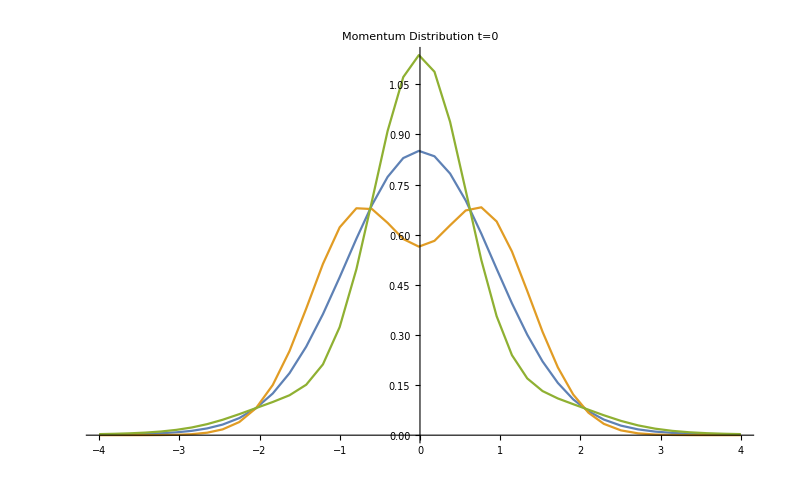

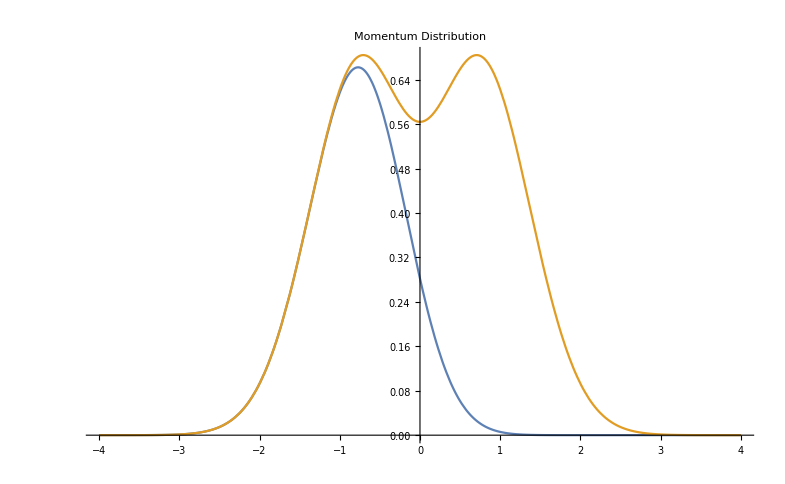

NIntegrate::inumr: The integrand (ⅇ^(-p^2-w^2) (2 ⅈ π (p^2+w^2) (Erfi[(p+Times[«2»])/(√2)]-Erfi[Power[«2»] Plus[«2»]])+4 ⅇ^(1/2 (p-w) (p+w)) √(2 π) (w Cos[p w]-p Sin[p w])))/π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{0.5*(Subscript[n, F][p]+Subscript[n, B][p,0]),Subscript[n, F][p],Subscript[n, B][p,0]},{p,-4,4},PlotLabel->"Momentum Distribution t=0",PlotRange->All,PlotPoints->6,MaxRecursion->3]
Plot[{0.5*(+h[p]+Subscript[n, F][p]),Subscript[n, F][p]},{p,-4,4},PlotRange->All,PlotPoints->6,MaxRecursion->8,PlotLabel->"Momentum Distribution"]
Plot[{Subscript[ρ, F][x,x]+Subscript[n, M][x] },{x,-4,4},PlotRange->All,PlotPoints->6,MaxRecursion->8,PlotLabel->"Prb Density in Position Space"]
```

```mathematica
Subscript[ρ, M][x_,y_]=(ⅇ^(1/2 (-x^2-3 y^2)) (-2 x-ⅇ^(y^2) √π (1+2 xy) Erf[y]))/(2 π);
Subscript[n, M][p_]=Integrate[E^(I*p(x-y))*Subscript[ψ, F][x,y,0]Abs[Subscript[ψ, F][x,y,0]],{x,-∞, ∞},{y,-∞, ∞},Assumptions->{Im[p]==0}]
```

Integrate[-(ⅇ^(-1/2 (p-ⅈ y) (p+3 ⅈ y)) (2 ⅈ p+ⅇ^(y^2) √π (1+2 xy) Erf[y]))/(√(2 π)),{y,-∞,∞},Assumptions→{Im[p]==0}]

```mathematica
Integrate[E^(I*p(x-y))*(Subscript[ψ, F][x,w,0]Abs[Subscript[ψ, F][y,w,0]]+Abs[Subscript[ψ, F][x,w,0]]Subscript[ψ, F][y,w,0]),{x,-∞, ∞},{y,-∞, ∞},Assumptions->{Im[p]==0,Im[w]==0}]
```

(2 ⅇ^(-p^2-w^2) (-ⅈ ⅇ^(1/2 (p-ⅈ w)^2) p √(2 π)+ⅈ ⅇ^(1/2 (p+ⅈ w)^2) p √(2 π)+ⅇ^(1/2 (p-ⅈ w)^2) √(2 π) w+ⅇ^(1/2 (p+ⅈ w)^2) √(2 π) w+ⅈ p^2 π Erfi[(p-ⅈ w)/(√2)]+ⅈ π w^2 Erfi[(p-ⅈ w)/(√2)]-ⅈ p^2 π Erfi[(p+ⅈ w)/(√2)]-ⅈ π w^2 Erfi[(p+ⅈ w)/(√2)]))/π

```mathematica
%350//FullSimplify
```

(ⅇ^(-p^2-w^2) (2 ⅈ π (p^2+w^2) (Erfi[(p-ⅈ w)/(√2)]-Erfi[(p+ⅈ w)/(√2)])+4 ⅇ^(1/2 (p-w) (p+w)) √(2 π) (w Cos[p w]-p Sin[p w])))/π

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {-0.450425}. NIntegrate obtained 1.30475×10^-17-1.28359×10^-18 ⅈ and 7.55984×10^-17 for the integral and error estimates.

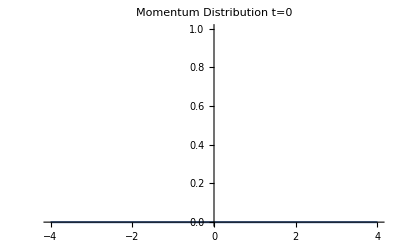

```mathematica
Subscript[n, M][p_]:=Abs[NIntegrate[%353,{w,-Infinity,Infinity}]];
Plot[Subscript[n, M][p],{p,-4,4},PlotLabel->"Momentum Distribution t=0",PlotRange->{0,1},PlotPoints->7,MaxRecursion->3]
```